## Computing p(χ_eff = 0) with numerical values Maria Okounkova

```mathematica
First let's compute p(Subscript[χ, eff]| q, ℳ) = 0
```

#### χ_eff in terms of {q, ℳ}

```mathematica
Solutionm1m2 = Solve[((m1*m2)^(3/5) / (m1 + m2)^(1/5))== ℳ  &&  m1/m2 == q,{m1,m2}]
```

{{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(1/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(1/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(2/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(2/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→-(-1)^(3/5) q^(2/5) (1+q)^(1/5) ℳ,m2→-((-1)^(3/5) (1+q)^(1/5) ℳ)/q^(3/5)},{m1→(-1)^(4/5) q^(2/5) (1+q)^(1/5) ℳ,m2→((-1)^(4/5) (1+q)^(1/5) ℳ)/q^(3/5)}}

```mathematica
Subm1m2 = Solutionm1m2[[1]]
```

{m1→q^(2/5) (1+q)^(1/5) ℳ,m2→((1+q)^(1/5) ℳ)/q^(3/5)}

```mathematica
ChiEffectivem1m2 = (a1 * (Cos[θ1]/m1) + (a2 * Cos[θ2])/m2)/(m1 + m2)
```

((a1 Cos[θ1])/m1+(a2 Cos[θ2])/m2)/(m1+m2)

```mathematica
ChiEffectiveForAllq =ChiEffectivem1m2 /. Subm1m2 // FullSimplify
```

(q^(1/5) (a1 Cos[θ1]+a2 q Cos[θ2]))/((1+q)^(7/5) ℳ^2)

#### Prior distributions

```mathematica
Pa[a_] := 1
Pθ[θ_] := Sin[θ]/2
Pϕ[ϕ_] := 1/(2*Pi)
Pℳ[ℳ_] := 1/(40 - 25)
PriorProduct = Pa[a1]*Pa[a2]*Pθ[θ1]*Pθ[θ2]*Pϕ[ϕ1]*Pϕ[ϕ2] (*Pℳ[ℳ]*)
```

(Sin[θ1] Sin[θ2])/(16 π^2)

#### Conditional probability p(χ_eff = 0 | a_1, a_2, θ_1, θ_2, ϕ_1, ϕ_2, q, ℳ)

```mathematica
PChiEffGivenAllVariables = DiracDelta[ChiEffective]
```

DiracDelta[(0.378929 (a1 Cos[θ1]+1. a2 Cos[θ2]))/ℳ^2]

Use the identity δ(Ax) = δ(x) / |A| for scalar A 
(see https://en.wikipedia.org/wiki/Dirac_delta_function#Scaling_and_symmetry)

```mathematica
PChiEffGivenAllVariablesRescaled = (1+q)^(7/5) ℳ^2 / q^(1/5) * DiracDelta[(a1 Cos[θ1]+a2 q Cos[θ2])]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]])/q^(1/5)

#### Create integrand to compute the probability p(χ_eff = 0| q, ℳ)

```mathematica
Integrand = PChiEffGivenAllVariablesRescaled * PriorProduct
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(16 π^2 q^(1/5))

#### Analytically Integrate over ϕ_1, ϕ_2, ℳ, and θ_1

```mathematica
Integrandϕ = Integrate[Integrand, {ϕ1, 0, 2*Pi}, {ϕ2, 0, 2*Pi}]
```

((1+q)^(7/5) ℳ^2 DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(4 q^(1/5))

```mathematica
(*Integrandϕℳ = Integrate[Integrandϕ, {ℳ, 25, 40}]*)
```

(16125 (1+q)^(7/5) DiracDelta[a1 Cos[θ1]+a2 q Cos[θ2]] Sin[θ1] Sin[θ2])/(4 q^(1/5))

```mathematica
Integrandϕθ1 = Integrate[Integrandϕ , {θ1, 0, Pi}]
```

-((1+q)^(7/5) ℳ^2 (HeavisideTheta[-a1+a2 q Cos[θ2]]-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2])/(4 a1 q^(1/5))

```mathematica
(*Integrandϕℳθ1 = Integrate[Integrandϕℳ , {θ1, 0, Pi}]*)
```

-1/(4 a1 q^(1/5))16125 (1+q)^(7/5) (HeavisideTheta[-a1+a2 q Cos[θ2]]-HeavisideTheta[a1+a2 q Cos[θ2]]) Sin[θ2]

#### Set up to Integrate numerically

Let’s remove the coefficient in front to simplify things - we’ll multiply the result by it later

```mathematica
PChieffZeroGivenQ[qval_] := NIntegrate[(Integrandϕθ1/.{q-> qval, ℳ -> 1}), {θ1, 0.0, Pi}, {θ2, 0.0, Pi}, {a1, 0.0, 0.99}, {a2, 0.0, 0.99}]
```

```mathematica
Now let's compute p(Subscript[χ, eff] | q) = 0 for various values of q
```

We define q to be uniform in [0.2, 1.0]

```mathematica
qvals = Range[0.2, 1.0, 0.1]
```

{0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
PChieffGivenqvals = PChieffZeroGivenQ[qvals]
```

{10.629,7.73691,7.67154,7.67926,7.6979,7.79643,7.86911,7.95729,8.02136}

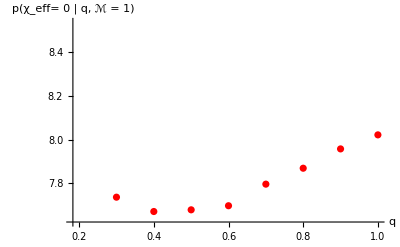

```mathematica
ListPlot[Transpose[{qvals,PChieffGivenqvals}], AxesLabel-> {"q", "p(χ_eff= 0 | q, ℳ = 1)"}, LabelStyle->Directive[Bold, Medium], PlotStyle->{Red, Thick}]
```